# Outer product の一般化

## MathematicaのOuter

Mathematicaには一般化された外積 Outer がある。

プロダクトの「リーフノード」の個数は、外積対象のオブジェクト数x各オブジェクトの「リーフノード」の数の積、となる一貫した定義である。

例 1)

```mathematica
ot1=Outer[List,{1,2},{3,4},{5,6}]
```

{{{{1,3,5},{1,3,6}},{{1,4,5},{1,4,6}}},{{{2,3,5},{2,3,6}},{{2,4,5},{2,4,6}}}}

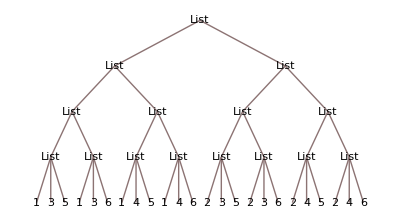

```mathematica
TreeForm[ot1]
```

```mathematica
Dimensions[ot1]
```

{2,2,2,3}

例 2)

```mathematica
ot2=Outer[List,{1,2},{3,4,5}]
```

{{{1,3},{1,4},{1,5}},{{2,3},{2,4},{2,5}}}

```mathematica
Dimensions[ot2]
```

{2,3,2}

例 3)

```mathematica
ot3=Outer[f,{1,2},{3,4,5}]
```

{{f[1,3],f[1,4],f[1,5]},{f[2,3],f[2,4],f[2,5]}}

```mathematica
Dimensions[ot3,AllowedHeads->All]
```

{2,3,2}

例 4)

ピックアップされるノードは、あくまでもリーフノードであり、木構造はその上位構造に反映される。

```mathematica
ot4=Outer[f,{1,2},{3,4,{5,6}}]
```

{{f[1,3],f[1,4],{f[1,5],f[1,6]}},{f[2,3],f[2,4],{f[2,5],f[2,6]}}}

```mathematica
Dimensions[ot4,AllowedHeads->All]
```

{2,3}

例 1~4を見るに、この外積の定義は、木構造の外積というよりは、リーフノード の外積とも言うべきものであり、しかも上位の木構造がプロダクトに反映されるという、一貫した美しさがある。

## 一般化された、木のOuter

MathematicaのOuterに対して、「木構造の外積」 とも言うべき別の外積の定義を考えてみた。

与えられたオブジェクト数の要素の組みを生成する

与えられたオブジェクトの構造を何らかの形でプロダクトに反映する

上記は、MathematicaのOuterの仕様でもある。

## 新しく定義した木のOuter

これを木構造の外積とするには、木の部分トラバースの組みを作る、というものとする。（他の定義も可能かも知れない）

たとえば、木A : A1[A2, A3]、木B : B1[B2,B3[B4]] としたとき、この二つのオブジェクトに対する外積を以下のような要素を基にして生成すると定義とする：
木Aの部分トラバースは、（根を出発点とする）、A1[A2,A3] ; A2 ; A3 の3要素、
木Bの部分トラバースは、（根を出発点とする）、B1[B2,B3[B4]] ; B2 ; B3[B4] ; B4 の4要素、となる。
このプロダクトは、「木の二つ組」が3x4=12組生成される。

上記に対して、そもそもMathematicaは式のOuterを許していないので、実行できない。
そこで別の言語に上記機能を実装する。

まず、Mathematicaによるオブジェクトの定義：

```mathematica
t5={A1[A2,A3],B1[B2,B3[B4]]}
```

{A1[A2,A3],B1[B2,B3[B4]]}

上記に対応するオリジナル言語の形式は以下となる：
 (A1(A2,A3),B1(B2,B3(B4))
 外積の定義は以下となる：
  $TO$(A1(A2,A3),B1(B2,B3(B4))

オリジナル言語のインタープリターを動作させる(to-test05.tq に上記式が記述されている)：
 $ tq in=to-test05.tq -FT -Pin -C                         
((A1(A2,A3),B1(B2,B3(B4))),(A2,B1(B2,B3(B4))),(A3,B1(B2,B3(B4))),(A1(A2,A3),B2),(A2,B2),(A3,B2),(A1(A2,A3),B3(B4)),(A2,B3(B4)),(A3,B3(B4)),(A1(A2,A3),B4),(A2,B4),(A3,B4))
8 Nodes were operated.

上記の二つの木のプロダクトを無理やりMathematica式にすると以下になる。

```mathematica
ot5=[[A1[A2,A3],B1[B2,B3[B4]]],[A2,B1[B2,B3[B4]]],[A3,B1[B2,B3[B4]]],[A1[A2,A3],B2],[A2,B2],[A3,B2],[A1[A2,A3],B3[B4]],[A2,B3[B4]],[A3,B3[B4]],[A1[A2,A3],B4],[A2,B4],[A3,B4]]
```

それでも不正なので、せいぜい、頑張って訳すと、、

```mathematica
ot5M={{A1[A2,A3],B1[B2,B3[B4]]},{A2,B1[B2,B3[B4]]},{A3,B1[B2,B3[B4]]},{A1[A2,A3],B2},{A2,B2},{A3,B2},{A1[A2,A3],B3[B4]},{A2,B3[B4]},{A3,B3[B4]},{A1[A2,A3],B4},{A2,B4},{A3,B4}}
```

{{A1[A2,A3],B1[B2,B3[B4]]},{A2,B1[B2,B3[B4]]},{A3,B1[B2,B3[B4]]},{A1[A2,A3],B2},{A2,B2},{A3,B2},{A1[A2,A3],B3[B4]},{A2,B3[B4]},{A3,B3[B4]},{A1[A2,A3],B4},{A2,B4},{A3,B4}}

```mathematica
Dimensions[ot5M]
```

{12,2}

二つ組が12個できている。

例をもう一つ：

$ echo '$TO$((1,2),(3,4),(5,6))' | tq in = /dev/stdin -FT -Pin -C
(((1, 2), (3, 4), (5, 6)), (1, (3, 4), (5, 6)), (2, (3, 4), (5, 6)), ((1, 2), 3, (5, 6)), (1, 3, (5, 6)), (2, 3, (5, 6)), ((1, 2), 4, (5, 6)), (1, 4, (5, 6)), (2, 4, (5, 6)), ((1, 2), (3, 4), 5), (1, (3, 4), 5), (2, (3, 4), 5), ((1, 2), 3, 5), (1, 3, 5), (2, 3, 5), ((1, 2), 4, 5), (1, 4, 5), (2, 4, 5), ((1, 2), (3, 4), 6), (1, (3, 4), 6), (2, (3, 4), 6), ((1, 2), 3, 6), (1, 3, 6), (2, 3, 6), ((1, 2), 4, 6), (1, 4, 6), (2, 4, 6))

```mathematica
ot6M={{{1,2},{3,4},{5,6}},{1,{3,4},{5,6}},{2,{3,4},{5,6}},{{1,2},3,{5,6}},{1,3,{5,6}},{2,3,{5,6}},{{1,2},4,{5,6}},{1,4,{5,6}},{2,4,{5,6}},{{1,2},{3,4},5},{1,{3,4},5},{2,{3,4},5},{{1,2},3,5},{1,3,5},{2,3,5},{{1,2},4,5},{1,4,5},{2,4,5},{{1,2},{3,4},6},{1,{3,4},6},{2,{3,4},6},{{1,2},3,6},{1,3,6},{2,3,6},{{1,2},4,6},{1,4,6},{2,4,6}}
```

{{{1,2},{3,4},{5,6}},{1,{3,4},{5,6}},{2,{3,4},{5,6}},{{1,2},3,{5,6}},{1,3,{5,6}},{2,3,{5,6}},{{1,2},4,{5,6}},{1,4,{5,6}},{2,4,{5,6}},{{1,2},{3,4},5},{1,{3,4},5},{2,{3,4},5},{{1,2},3,5},{1,3,5},{2,3,5},{{1,2},4,5},{1,4,5},{2,4,5},{{1,2},{3,4},6},{1,{3,4},6},{2,{3,4},6},{{1,2},3,6},{1,3,6},{2,3,6},{{1,2},4,6},{1,4,6},{2,4,6}}

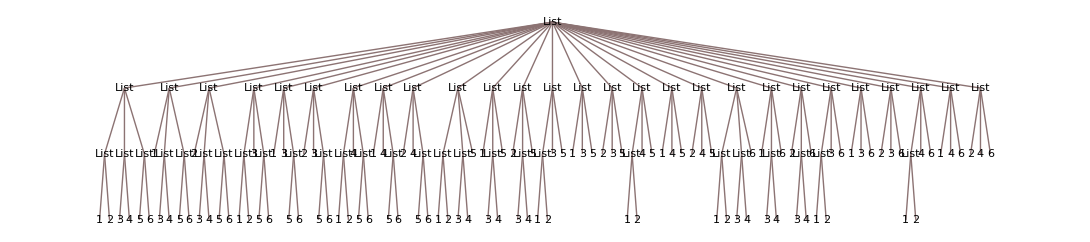

```mathematica
TreeForm[ot6M]
```

さらにもう一つ：

$ echo ‘$TO$((1,2),(3(4)))’|tq in=/dev/stdin -FT -Pin -C|tr ‘(‘ ‘{‘|tr ‘)’ ‘}’
7 Nodes were operated.
{{{1,2},{3{4}}},{1,{3{4}}},{2,{3{4}}},{{1,2},3{4}},{1,3{4}},{2,3{4}},{{1,2},4},{1,4},{2,4}}

```mathematica
tmp={{{1,2},{3{4}}},{1,{3{4}}},{2,{3{4}}},{{1,2},3{4}},{1,3{4}},{2,3{4}},{{1,2},4},{1,4},{2,4}}
```

{{{1,2},{{12}}},{1,{{12}}},{2,{{12}}},{{1,2},{12}},{1,{12}},{2,{12}},{{1,2},4},{1,4},{2,4}}

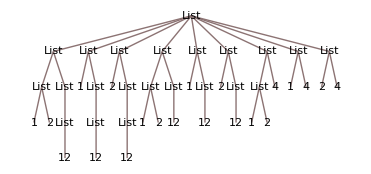
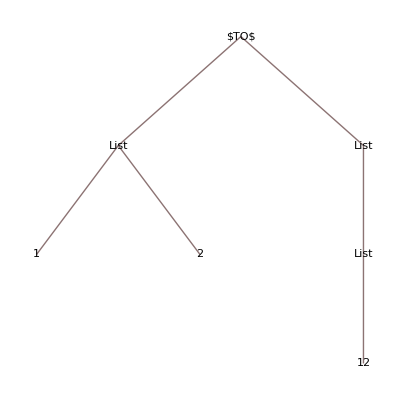

```mathematica
{TreeForm[tmp],TreeForm[$TO$[{1,2},{3{4}}]]}
```

MathematicaのOuterと異なるのは、
・二つ組の下に構造が反映される
・中間ノードも反映される（Headの制限がない）
・木のDepthが保存される（与えられた式の深さ+1の深さのプロダクトが返る）
ことである。

```mathematica
TreeForm[$TO$[{1,2},{3{4}}]]
```